```mathematica
(* Solving Friedmann eqn for 3 'easy' cases *)
(* Case 1: k=0, lambda=3 (nonzero), rho=m/a^3, c=1*)

(*I'm using simplified version of eqn that I worked on paper beforehand*)
(*Integrating this gives t as a function of a, t=...*)

integrate[((8*pi*G*(m/a)+3*a^2)/3)^(-1/2),a]
```

```mathematica
Integrate[(√3)/(√(3 a^2+(8 G m Pi)/a)),a]
```

```mathematica
(2 √a √(3 a^2+(8 G m π)/a) ArcTanh[a^(3/2)/(√(a^3+(8 G m π)/3))])/(3 √(3 a^3+8 G m π))
```

(2 √a √(3 a^2+(1.67738×10^-9 m)/a) ArcTanh[a^(3/2)/(√(a^3+5.59126×10^-10 m))])/(3 √(3 a^3+1.67738×10^-9 m))

```mathematica
(* Use Solve to invert eqn and solve for a(t)*)
(* Define variables*)

G=6.67408*10^(-11)  (* m^3 kg^-1 s^-2 *)
```

```mathematica
Solve[t==(2 √a √(3 a^2+(8 G m π)/a) ArcTanh[a^(3/2)/(√(a^3+(8 G m π)/3))])/(3 √(3 a^3+8 G m π)),a]
```

```mathematica
{{a->-(2 G^(1/3) m^(1/3) (-π/3)^(1/3) Tanh[(3 t)/2]^(2/3))/((1-Tanh[(3 t)/2]^2)^(1/3))},{a->(2 G^(1/3) m^(1/3) (π/3)^(1/3) Tanh[(3 t)/2]^(2/3))/((1-Tanh[(3 t)/2]^2)^(1/3))},{a->(2 (-1)^(2/3) G^(1/3) m^(1/3) (π/3)^(1/3) Tanh[(3 t)/2]^(2/3))/((1-Tanh[(3 t)/2]^2)^(1/3))}}
```

{{a→-((0.000411914+0.000713456 ⅈ) m^(1/3) Tanh[(3. a √(1.+(1.7885×10^9 a)/m) Hypergeometric2F1[0.5,0.5,1.5,-(1.7885×10^9 a)/m])/(√(a (a+5.59126×10^-10 m)))]^(2/3))/((1-Tanh[(3. a √(1.+(1.7885×10^9 a)/m) Hypergeometric2F1[0.5,0.5,1.5,-(1.7885×10^9 a)/m])/(√(a (a+5.59126×10^-10 m)))]^2)^(1/3))},{a→(0.000823828 m^(1/3) Tanh[(3. a √(1.+(1.7885×10^9 a)/m) Hypergeometric2F1[0.5,0.5,1.5,-(1.7885×10^9 a)/m])/(√(a (a+5.59126×10^-10 m)))]^(2/3))/((1-Tanh[(3. a √(1.+(1.7885×10^9 a)/m) Hypergeometric2F1[0.5,0.5,1.5,-(1.7885×10^9 a)/m])/(√(a (a+5.59126×10^-10 m)))]^2)^(1/3))},{a→-((0.000411914-0.000713456 ⅈ) m^(1/3) Tanh[(3. a √(1.+(1.7885×10^9 a)/m) Hypergeometric2F1[0.5,0.5,1.5,-(1.7885×10^9 a)/m])/(√(a (a+5.59126×10^-10 m)))]^(2/3))/((1-Tanh[(3. a √(1.+(1.7885×10^9 a)/m) Hypergeometric2F1[0.5,0.5,1.5,-(1.7885×10^9 a)/m])/(√(a (a+5.59126×10^-10 m)))]^2)^(1/3))}}

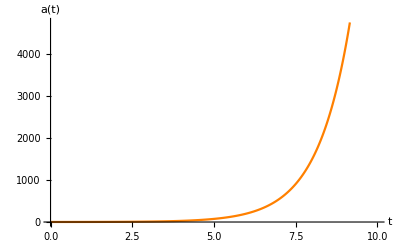

```mathematica
(* Plot a(t) and compare to mcguigan*)

Plot[{Cosh[t],(0.0008238282323528803 m^(1/3) Tanh[(3. a √(1.+(1.7885042930099957*^9 a)/m) Hypergeometric2F1[0.5,0.5,1.5,-(1.7885042930099957*^9 a)/m])/(√(a (a+5.59126418599215*^-10 m)))]^(2/3))/((1-Tanh[(3. a √(1.+(1.7885042930099957*^9 a)/m) Hypergeometric2F1[0.5,0.5,1.5,-(1.7885042930099957*^9 a)/m])/(√(a (a+5.59126418599215*^-10 m)))]^2)^(1/3))},{t,0,10}, BaseStyle->{FontWeight-> "Bold", FontSize-> 12},
AxesLabel-> {"t","a(t)"}, PlotPoints-> 1000, PlotStyle-> {Orange,Thick}]
```